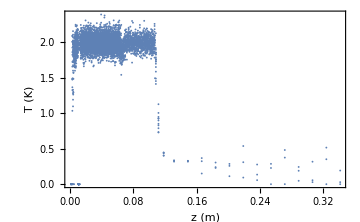
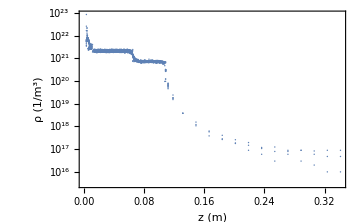
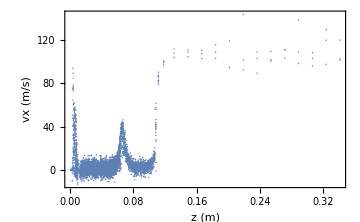

```mathematica
d=Import["/home/cal/Documents/DSMC_Simulations/6_10_20_fixed_collisions/flow_4.00000_gap_0.00200_len_0.04000_T1_2.00000_T2_2.00000/data/DS2FF.DAT","Table",HeaderLines->9];dcenter=Select[d,#[[2]]<0.004&];
x=dcenter[[;;,1]];
y=dcenter[[;;,2]];
T=dcenter[[;;,3]];
ρ=dcenter[[;;,4]];
vx=dcenter[[;;,6]];
vy=dcenter[[;;,7]];
Row[{ListPlot[Transpose@{x,T},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"z (m)","T (K)",None,None},ImageSize->Medium],
ListLogPlot[Transpose@{x,ρ},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"z (m)","ρ (1/m^3)",None,None},ImageSize->Medium],
ListPlot[Transpose@{x,vx},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"z (m)","vx (m/s)",None,None},ImageSize->Medium]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

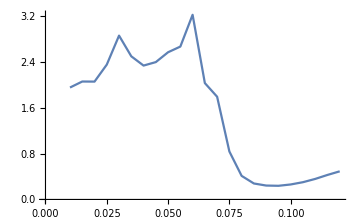

```mathematica
dinterp=Interpolation[Transpose@{Transpose@{x,y},ρ vx/(4.4803*10^17)},InterpolationOrder->1];
xinterp=Table[x,{x,0.01,0.12,0.005}];
fluxint=Table[NIntegrate[2π r dinterp[xx,r],{r,0,0.004},MaxRecursion->100],{xx,xinterp}];
ListLinePlot[Transpose@{xinterp,fluxint},ImageSize->Medium]
```